Andrea Halenkamp
4/26/2017

# Part VI

Consider the following predator-prey system:
x'=9x-α*x^2-3x*y
y'=-2y+x*y
Where 0 ≤ α ≤ 5

### Find Equilibrium Points

```mathematica
Clear[α];
Solve[{9x-α*x^2-3x*y==0,-2y+x*y==0},{x,y}]
```

{{x→2,y→1/3 (9-2 α)},{x→0,y→0},{x→9/α,y→0}}

Found three points: (2,1/3 (9-2 α)),(0,0), (9/α,0)

#### Find when points coalesce

Set first point found equal to second point found

```mathematica
Solve[{2==9/α,1/3 (9-2 α)==0},α]
```

{{α→9/2}}

#### Equilibrium Quadrants

Plot how α changes the points

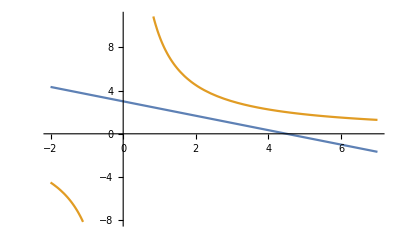

```mathematica
Plot[{1/3 (9-2 α),9/α},{α,-2,7}]
```

Note where α changes value from positive to negative for each equation.

#### When α = 0

Find Equilibrium points of equation at α = 0

```mathematica
Solve[{9x-0*x^2-3x*y==0,-2y+x*y==0},{x,y}]
```

{{x→0,y→0},{x→2,y→3}}

Looking at previous points (2,1/3 (9-2 α)),(0,0), (9/α,0)
The last point divides by α, and when it is zero becomes undefined. Leaving (2,1/3 (9-2 α)),(0,0) which end up turning into (2,3),(0,0)

### Summarize Equilibrium Points

Establish equations

```mathematica
f[x_,y_]:=9x-α*x^2-3x*y;
g[x_,y_]:=-2y+x*y;
```

Jacobian Equation

```mathematica
j[x_,y_]={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}};
```

#### Equilibrium Point (0,0)

Compute the trace and the determinant of the Jacobian evaluated at the equilibrium point.

```mathematica
j[0,0]
```

{{9,0},{0,-2}}

```mathematica
Det[j[0,0]]
```

-18

```mathematica
Tr[j[0,0]]
```

7

Equilibrium type is always a Saddle

#### Equilibrium Point (2,1/3 (9-2 α))

Compute the trace and the determinant of the Jacobian evaluated at the equilibrium point.

```mathematica
j[2,1/3 (9-2 α)]
```

{{-2 α,-6},{1/3 (9-2 α),0}}

```mathematica
Det[j[2,1/3 (9-2 α)]]
```

18-4 α

```mathematica
Tr[j[2,1/3 (9-2 α)]]
```

-2 α

```mathematica
TableForm[{{"α","<0","0<x<4.5","=4.5",">4.5"},{"Determinant","+","+","-","-"},{"Trace","+","-","-","-"}}]
```

α | <0 | 0<x<4.5 | =4.5 | >4.5
Determinant | + | + | - | -
Trace | + | - | - | -

#### Equilibrium Point (9/α,0)

Compute the trace and the determinant of the Jacobian evaluated at the equilibrium point.

```mathematica
j[9/α,0]
```

{{-9,-27/α},{0,-2+9/α}}

```mathematica
Det[j[9/α,0]]
```

18-81/α

```mathematica
Tr[j[9/α,0]]
```

-11+9/α

```mathematica
TableForm[{{"α","<9/11","=9/11","9/11<x<4.5","=4.5",">4.5"},{"Determinant","-","-","-","0","+"},{"Trace","+","0","-","-","-"}}]
```

α | <9/11 | =9/11 | 9/11<x<4.5 | =4.5 | >4.5
Determinant | - | - | - | 0 | +
Trace | + | 0 | - | - | -

#### Vector Plot

```mathematica
Manipulate[VectorPlot[{9x-a*x^2-3x*y,-2y+x*y},{x,-5,10},{y,-5,10},Axes->True,Frame->True,VectorScale->{Tiny,Automatic,None},VectorStyle->Arrowheads[.02],VectorPoints->Fine],{a,-2,7,1}]
```

#### Bifurcation Values

Point 1: Create a chart with values for α with their corresponding determinants and traces

```mathematica
TableForm[Table[{α,Det[j[2,1/3 (9-2 α)]],Tr[j[2,1/3 (9-2 α)]]},{α,-1,5}]]
```

-1 | 22 | 2
0 | 18 | 0
1 | 14 | -2
2 | 10 | -4
3 | 6 | -6
4 | 2 | -8
5 | -2 | -10

Make a plot of K = (tr(J))^2+4det(J)

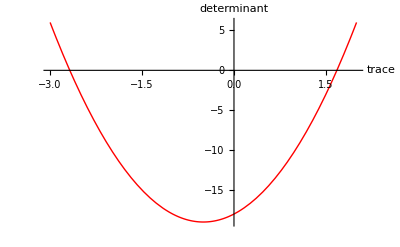

```mathematica
Plot[Tr[j[2,1/3 (9-2 α)]]^2-Det[j[2,1/3 (9-2 α)]],{α,-3,2},PlotStyle->{Thick,Red},AxesLabel->{"trace","determinant"}]
```

```mathematica
NSolve[Tr[j[2,1/3 (9-2 α)]]^2-Det[j[2,1/3 (9-2 α)]]==0,α]
```

{{α→-2.67945},{α→1.67945}}

Point 2: Create a chart with values for α with their corresponding determinants and traces

```mathematica
TableForm[Table[{α,Det[j[9/α,0]],Tr[j[9/α,0]]},{α,1,5}]]
```

1 | -63 | -2
2 | -45/2 | -13/2
3 | -9 | -8
4 | -9/4 | -35/4
5 | 9/5 | -46/5

Make a plot of K = (tr(J))^2+4det(J)

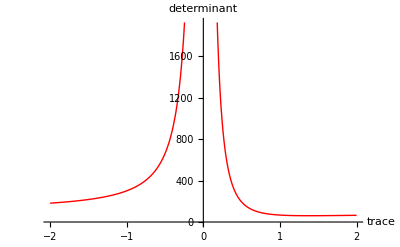

```mathematica
Plot[Tr[j[9/α,0]]^2-Det[j[9/α,0]],{α,-2,2},PlotStyle->{Thick,Red},AxesLabel->{"trace","determinant"}]
```

I used the above to try and figure out the values of the bifurcation points. In the end, I simply looked at the changes in equilibrium types based on α and used those points as the bifurcation points.

### Interpret Results

Assuming we are only interested in quadrant I, the only real values for predator and prey populations. When there is a high amount of prey, predators start to rise, when there are a lot of predators, prey begins to fall. These values balance around the point (2, 1/3 (9-2 α)). If there are too many predators, the prey will fall fast enough to approach 0, and then the predators will approach 0 and end up at the point (0,0). If there are no predators, prey will continue to rise until they reach the point (9/α, 0). If  is negative (If possible) then prey will rise forever when there are no predators. If  is high enough, then instead of constantly going up and down, the balance would immediately go to the point and stay there.

It seems to be that the point (2, 1/3 (9-2 α)) is what is described as the happy equilibrium, where predators and prey are balancing each other out and neither is losing too much of it’s population to not be able to recover. The equilibrium point (0,0) is obviously when the two populations die out, either by too many predators and just not enough prey or starting out with neither. The other equilibrium point (9/α, 0) seems to be a resource restriction for solely prey, as it does not seem to affect predators in any way.